## Set up

```mathematica
alpha=2;
l=16;
hd="/Users/keitokiddo/VC_revision/Simulations/";
fl="2_16_SPR";
wd=StringJoin[hd,fl];
SetDirectory[wd];
```

```mathematica
nrep=3;
nprop=13;
schemes={"random","noised","mut"};
nschemes=Length@schemes;
```

```mathematica
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}]; 
wt=ConstantArray[0,l];
AA={"A","C","G","T"};
AAtoDigitRules = {"A"->0,"C"->1,"G"->2,"T"->3};
DigitToAARules = {0->"A",1->"C",2->"G",3->"T"};
sequencesAA=StringJoin[#/.DigitToAARules]&/@sequences;
wtAA = sequencesAA[[1]];
mks=Table[Binomial[l,k](alpha-1)^k, {k,0,l}];
```

```mathematica
MakeLapRec[alpha_,l_]:=Module[{L1,L,m},
L1 = SparseArray[alpha*IdentityMatrix[alpha] - ArrayReshape[ConstantArray[1,alpha^2],{alpha,alpha}]];
m=1;
L=L1;
While[m<l, L = KroneckerProduct[L, IdentityMatrix[alpha]] + KroneckerProduct[IdentityMatrix[alpha^m],L1];
m++];
L
]
L=MakeLapRec[alpha,l];//AbsoluteTiming
```

{15.5364,Null}

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

#### Export design matrix for glmnet

```mathematica
(*varall = ConstantArray[0, alpha^l];*)
```

```mathematica
(*designAllonehot=s2donehot[sequences,Range[0,l]];//AbsoluteTiming*)
```

```mathematica
(*rules=Flatten[Table[Join[Table[designrules[sequences[[j]],k,wt,j],{k,3}]],{j,Length[sequences]}],2];
null3=SparseArray[rules,{Length[sequences],Total@Table[Binomial[l, k]*(alpha - 1)^k,{k,0,3}]}];
Export["data/rules.tsv",Transpose@{Most[ArrayRules[null3]][[All,1]][[All,1]],Most[ArrayRules[null3]][[All,1]][[All,2]]},"TSV"];*)
```

### Import FL

```mathematica
fs=Table[{},nrep];
Do[fs[[i]]=Import[StringJoin["data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
fns=Table[{},nrep];
Do[fns[[i]]=Import[StringJoin["data/",fl,  "_f_","noised_", ToString[i],"_","0.2",".tsv"]]//Flatten,{i,nrep}];
```

### Import training samples

```mathematica
trs=Table[{},Length@proportions];
Do[trs[[i]]=Import[StringJoin["data/", "tr_",ToString[i],".tsv"]]//Flatten,{i,Length@proportions}]
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
```

```mathematica
trsmut=Table[{},Length@proportions];
Do[trsmut[[i]]=Import[StringJoin["data/", "tr_mut_",ToString[i],".tsv"]]//Flatten,{i,Length@trsmut}]
ttsmut=Table[Complement[Range[alpha^l],trsmut[[i]]],{i,Length[trsmut]}];
```

## *Functions

### Basic functions

```mathematica
dp[v_]:=v//DeleteDuplicates
uqc[v_]:=v//DeleteDuplicates//Length
lg[v_]:=v//Length
dim[m_]:=m//Dimensions
```

```mathematica
seq2posAA[seqAA_]:=seq2pos[Characters[seqAA]/.AAtoDigitRules]
```

```mathematica
associate0[list_,obj_]:=Table[list[[i]]->obj,{i,Length[list]}]
```

```mathematica
MakeDiagonal[vect_]:= SparseArray[Table[{i,i}->vect[[i]],{i,Length[vect]}]]
```

```mathematica
Nbysum[y_]:=(1/Total[y])*y
Nbyfirst[y_]:=(1/First@y)*y
```

```mathematica
ginv[x_]:=If[N[x]==0.,0,1/x]
```

```mathematica
r2[x_, y_] := If[Length@x<2, {}, Correlation[x, y]^2];


mse[x_, y_] := Mean[(x - y)^2];
maxorder[list_] := 
  Module[{i}, 
   For[i = 1, list[[i ;;]] != ConstantArray[0, Length[list[[i ;;]]]], 
    i++]; i - 1];

(*From sequence to lexicographical position*)

seq2pos[seq_] := FromDigits[seq, alpha] + 1

(*Map a vector of length m to a vector of length alpha^l. "list" contains the lexicographical positions for all sequences in "data"*)MapPartialVal[list_,data_,height_]:=Module[{Ab},Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{height,Length[list]}];Ab.data]
```

### Projection operators

```mathematica
Pby[x_,Pcoeffs_]:=Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1];
```

```mathematica
Pkby[x_,k_]:=Module[{Pcoeffs},Pcoeffs=Inverse[LPs].wkd[[All,k+1]];Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1]];
```

### Regression functions

```mathematica
(*Ridge regression with regularization parameter "Î»" and design matrix "design"*)

RidgeRegression[design_, response_, Î»_] := Module[{cross},
  cross = Transpose[design].design;
  Do[cross[[i, i]] += Î»^2, {i, Length[cross]}];
  LinearSolve[cross,
   Transpose[design].response,
   Method -> {"Krylov", "Method" -> "ConjugateGradient", 
     "Preconditioner" -> "ILU0"}]]

(*Ordinary least square regression*)

OrdinaryRegression[design_, response_] := Module[{cross},
  cross = Transpose[design].design;
  LinearSolve[cross, Transpose[design].response, Method -> "Krylov"]]

(*Build design vector for a sequence using the Taylor encoding*)

s2dTaylor[seq_, order_, wt_] := Module[{seqprime, sub1, sub2, pos},
  seqprime = Mod[seq - wt, alpha];
  sub1 = Subsets[seqprime, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] - 1, alpha - 1] + 
      1 + (#[[1]] - 1)*((alpha - 1)^order) & /@ 
    Select[sub2, ! MemberQ[#, 0] &];
  SparseArray[
   Table[pos[[i]] -> 1, {i, 
     Length[pos]}], {Binomial[l, order]*(alpha - 1)^order}]
  ]
(*Build design vector for sequence using the one-hot encoding*)

s2d[seq_, order_] := Module[{sub1, sub2, pos},
  sub1 = Subsets[seq, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#], alpha] + 
      1 + (#[[1]] - 1)*(alpha^order) & /@ sub2;
  SparseArray[
   Table[pos[[i]] -> 1, {i, 
     Length[pos]}], {Binomial[l, order]*(alpha)^order}]
  ]

designrules[seq_, order_, wt_,j_]:=Module[{seqprime, sub1, sub2, pos},
  seqprime = Mod[seq - wt, alpha];
  sub1 = Subsets[seqprime, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] - 1, alpha - 1] + 
      1 + (#[[1]] - 1)*((alpha - 1)^order)+ Total@Table[Binomial[l,k](alpha-1)^(k),{k,0,order-1}]& /@ 
    Select[sub2, ! MemberQ[#, 0] &];
  Table[{j,pos[[i]]} -> 1, {i, 
     Length[pos]}]
  ]
s2dTaylor2[seqs_,order_,wt_]:=Module[{rules},rules=Flatten[Table[Join[Table[designrules[seqs[[j]],k,wt,j],{k,order}]],{j,Length[seqs]}],2];SparseArray[rules,{Length[seqs],Total@Table[Binomial[l, k]*(alpha - 1)^k,{k,order}]}]]
```

### Kernelized regressions

```mathematica
CIby[x_]:={0,-alpha/2,1/2}.NestList[L.#&,x,2](*Similar to C.f, we implement multiplication by a matrix that can be expressed as a polynomial in L using NestList.*)(*coeffsinLn: vector of coefficients for L^n*)
SprsinLnBy[x_,coeffsinLn_]:=coeffsinLn[[1;;maxorder[coeffsinLn]]].NestList[L.#&,x,maxorder[coeffsinLn]-1](*Apply the locally non-epistatic smoother M to a vector*)
Smooth[x_]:=-(1/(Binomial[l,2](alpha-1)^2))CIby[x]+x(*Calculate the average squared epistasic coefficient for a vector x*)
Cnorm[x_]:=(1/(nfaces))x.CIby[x]
```

```mathematica
(*Multiplication by the C matrix defined in the main text. For the matrix by vector multiplication C.f, we evaluate it as {0,-alpha/2,1/2}.{f,L.f,L.L.f} using the function NestList. Note that we have omitted the constant 1/s, since it does not affect the solution to the linear equation*)
(*Minimum epistasis interpolation solver*)
Cinterp[training_,y_]:=Module[{Ai,Ab},Ai=SparseArray[Transpose[{Complement[Range[1,alpha^l],training],Range[1,alpha^l-Length[training]]}]->1,{alpha^l,alpha^l-Length[training]}];Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];(Ai.LinearSolve[Transpose[Ai].CIby[Ai.#]&,-Transpose[Ai].CIby[Ab.y],Method->{"Krylov",Method->"ConjugateGradient",Tolerance->10^-15}])+Ab.y](*Regularized regression with regularization parameter given by "rp". "Ccoeffs" and "Pcoeffs" contain entries for a general cost matrix C (not necessarily the C used in the minimum epistasis interpolation problem) and projection matrix P each of which is represented as the coefficients of a polynomial in L. "Ccoeffs" and "Pcoeffs" for fitting models of different orders are defined below*)
Creg[Ccoeffs_,Pcoeffs_,training_,data_,rp_,var_,startingvector_]:=Module[{Ab,W,Cby,Pby},W=(1/Length[data]) SparseArray[Table[{training[[i]],training[[i]]}->(1/var[[i]]),{i,Length[training]}],{alpha^l,alpha^l}];Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];Cby[x_]:=rp*Ccoeffs[[1;;maxorder[Ccoeffs]]].NestList[L.#&,x,maxorder[Ccoeffs]-1];Pby[x_]:=Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1];LinearSolve[(Cby[#]+Pby[W.Pby[#]])&,Pby[W.Ab.data],Method->{"Krylov",Method->"ConjugateGradient","StartingVector"->If[Length[startingvector]==0,ConstantArray[0,alpha^l],startingvector]}]]

(*10-fold crossvalidation using the function Creg*)CrossvalidationC[Ccoeffs_,Pcoeffs_,list_,response_,rps_,variance_,fold_,rep_]:=Module[{size,subsets,r,rpsr},
size=Ceiling[Length[response]/fold]; 
subsets=Partition[RandomSample[Range[1,Length[response]]],size,size,1,{}];r=Table[Table[{},Length[rps]+1],rep];Do[Do[r[[k]][[i+1]]=Creg[Ccoeffs,Pcoeffs,list[[Flatten[Drop[subsets,{k}]]]],response[[Flatten[Drop[subsets,{k}]]]],rps[[i]],variance[[Flatten[Drop[subsets,{k}]]]],{}],{i,Length[rps]}],{k,rep}];Table[mse[r[[k]][[i+1]][[list[[subsets[[k]]]]]],response[[subsets[[k]]]]]
,{k,rep},{i,Length[rps]}]
]

(*Extract best regularization parameter from the crossvalidation outputs*)CV[mse_,rps_]:=Module[{means,ses,min,bestlambda},means=Mean[mse];ses=If[Dimensions[mse][[1]]>1,StandardDeviation[mse]/√(Dimensions[mse][[1]]),ConstantArray[0,Dimensions[mse][[2]]]];min=First[Ordering[means]];bestlambda=rps[[min ]];{bestlambda,means,ses}]
```

### Matrix coefficients

```mathematica
(*Krawtchouk polynomial*)
w[alpha_, k_, d_] := alpha^(-l) ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q]
wkd = Table[w[alpha,k,d],{d,0,l},{k,0,l}];
```

```mathematica
(*LPs contains entries of L^n defined at d=0,1,...l. For any matrix whose (i,j)-th entry only depends on d(i,j), we can then solve a linear equation for the coefficients*)
B=SparseArray[{i_,i_}->(alpha-1)*l,{l+1,l+1}]-1*(SparseArray[{i_,j_}/;i==j:>(i-1)*(alpha-2),{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==1:>i-1,{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==-1:>(l-j+2)*(alpha-1),{l+1,l+1}]);
LPs=ArrayReshape[{PadRight[{1},l+1],PadRight[{(alpha-1)*l,-1},l+1],Table[MatrixPower[B,i].PadRight[{(alpha-1)*l,-1},l+1],{i,1,l-1}]},{l+1,l+1}]//Transpose;

(*Entries of the pseudo-inverse of the interpolation matrix C*)
KIentries=Table[ReleaseHold[Hold[∑_(k=2)^length (alpha^(-l)  1/(((a k)^2-a(a k))a^length)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for pairwise regression*)
C2entries=Table[ReleaseHold[Hold[∑_(k=2)^2 (alpha^(-l)  ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for three-way regression*)
C3entries=Table[ReleaseHold[Hold[∑_(k=2)^3 (alpha^(-l)  ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];
(*Entries of the cost matrix for the Additive model*)
P1entries=Table[ReleaseHold[Hold[∑_(k=0)^1 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for the Pairwise model*)
P2entries=Table[ReleaseHold[Hold[∑_(k=0)^2 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for the Three-way model*)
P3entries=Table[ReleaseHold[Hold[∑_(k=0)^3 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];
(*Coefficients for the interpolation matrix C in L*)
CIinLn=PadRight[{0,-alpha/2,1/2},l+1];

(*Coefficients for the interpolation kernel matrix K in L*)
KIinLn=Inverse[LPs].KIentries;

(*Coefficients for the cost matrix for the Pairwise model in L*)
C2inLn=Inverse[LPs].C2entries;

(*Coefficients for the cost matrix for the Three-way model in L*)
C3inLn=Inverse[LPs].C3entries;

(*Coefficients for the projection matrix for the Three-way model in L*)
P3inLn=Inverse[LPs].P3entries;

(*Coefficients for the projection matrix for the Pairwise model in L*)
P2inLn=Inverse[LPs].P2entries;

(*Coefficients for the projection matrix for the Additive model in L*)
P1inLn=Inverse[LPs].P1entries;
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

### Build matrices

```mathematica
(*(*Build graph Laplacian of the sequence space. L is a sparse matrix with sparsity = 1 - ((alpha-1)l+1)/(alpha^l). Therefore we'll use it to facilitate fast solution of most linear equations in this notebook*)
MakeLaplacian[A_,l_]:=SparseArray[Join[ParallelTable[{i,i}->l(A-1),{i,1,A^l}],Flatten[ParallelTable[{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->-1,{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]]*)
```

```mathematica
(*AbsoluteTiming[L=MakeLaplacian[alpha,l];]*)
```

```mathematica
(*MakeAdj[A_,l_]:=SparseArray[Flatten[ParallelTable[{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->1,{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]*)
```

```mathematica
(*Adj=MakeAdj[alpha,l];//AbsoluteTiming*)
```

```mathematica
(*Adj = -(L - SparseArray[Flatten[Table[{i,i}->(alpha-1)*l,{i,1,alpha^l}],2]]);*)
```

```mathematica
(*null = Table[
   Join[s2dTaylor[sequences[[i]], 0, wt], 
    s2dTaylor[sequences[[i]], 1, wt]], {i, Length[sequences]}];//AbsoluteTiming*)
```

```mathematica
(*null2=SparseArray[Table[Join[s2dTaylor[seq,0,wt],s2dTaylor[seq,1,wt],s2dTaylor[seq,2,wt]],{seq,sequences}]];//AbsoluteTiming*)
```

```mathematica
designrulesonehot[seq_, order_,j_]:=Module[{ sub1, sub2, pos},

  sub1 = Subsets[seq, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] , alpha ] + 
      1 + (#[[1]]-1 )*((alpha )^order)+ Total@Table[Binomial[l,k](alpha)^(k),{k,0,order-1}]& /@ 
    sub2;
  Table[{j,pos[[i]]} -> 1, {i, 
     Length[pos]}]
  ]
s2donehot[seqs_,order_]:=Module[{rules},rules=Flatten[Table[Join[Table[designrulesonehot[seqs[[j]],k,j],{k,order}]],{j,Length[seqs]}],2];SparseArray[rules,{Length[seqs],Total@Table[Binomial[l, k]*(alpha ^k),{k,order}]}]]
```

```mathematica
rules=Flatten[Table[Join[Table[designrulesonehot[sequences[[j]],k,j],{k,0, 1}]],{j,Length[sequences]}],2];//AbsoluteTiming
```

{9.93044,Null}

```mathematica
nullonehot=SparseArray[rules,{Length[sequences],Total@Table[Binomial[l, k]*(alpha)^k,{k,0,1}]}];
```

## Simulate

### Simulate landscapes by sampling columns of design matrix

```mathematica
associate[tab_]:=tab->1
weights=Table[Binomial[l,k](alpha)^k, {k,0,l}];
s=.1;
m=Round[s*Total[mks]];
```

```mathematica
rules=Table[{},m];
Do[
Module[
{order, sites, pos},
order=RandomSample[weights->Range[0,l],1][[1]];
sites=RandomSample[Range[l], order];pos = FromDigits[#,alpha]&/@Tuples@ReplacePart[ConstantArray[A, l],Table[site->{RandomChoice[A]}, {site,sites}]]+1;
rules[[i]]=associate[#]&/@Transpose@{ConstantArray[i, Length@pos],pos};
], {i, m}]//AbsoluteTiming
```

{2.26274,Null}

```mathematica
rules=Flatten[rules,1];
designmatrix=SparseArray[rules,{m,alpha^l}];
designmatrix = Transpose@designmatrix;
```

```mathematica
nrep=3;
fs=Table[Module[{beta},beta=RandomVariate[NormalDistribution[0,1],m];
designmatrix.beta],nrep];
Do[fs[[i]]=fs[[i]]/StandardDeviation[fs[[i]]],{i,nrep}]
Do[Export[StringJoin["data/",fl,"_f_",ToString[i],".tsv"],fs[[i]],"TSV"],{i,nrep}]
```

```mathematica
ldaObs=Table[Norm[Pkby[fs[[j]],k]]^2/mks[[k+1]],{j,nrep},{k,1,l}];
```

```mathematica
Mean[Nbyfirst/@ldaObs]
```

{1.,0.455432,0.126969,0.0421818,0.0146131,0.00477061,0.00160408,0.000524641,0.000176694,0.0000593638,0.0000198582,6.51296×10^-6,2.21082×10^-6,7.85253×10^-7,3.26932×10^-7,3.03631×10^-7}

```mathematica
VCObs=Table[Nbysum[Rest@mks*ldaObs[[i]]],{i,nrep}]//N
```

{{0.0632635,0.169312,0.184371,0.232469,0.172435,0.103929,0.048943,0.0181648,0.0055229,0.00130449,0.000249525,0.0000324612,3.4679×10^-6,3.41646×10^-7,2.37897×10^-8,1.57522×10^-9},{0.0338438,0.148873,0.207056,0.217468,0.194201,0.114154,0.056005,0.0204339,0.00622112,0.00144159,0.000261857,0.0000364345,3.68278×10^-6,2.67104×10^-7,8.88503×10^-9,1.98328×10^-10},{0.0501406,0.15905,0.215576,0.215319,0.175706,0.107667,0.0507573,0.018809,0.0054097,0.00129962,0.000229765,0.0000317333,3.43477×10^-6,2.19393×10^-7,1.71593×10^-8,1.31225×10^-9}}

```mathematica
lambdaExpected=(1/m)*Table[2^(l-i) (1 + (alpha-1)*.5)^(l-i),{i,1,l}]//N;
```

```mathematica
Export["tru_lda.tsv",lambdaExpected]
```

tru_lda.tsv

```mathematica
(*Analytical results of variance components under sparse one-hot basis*)
VCExpected=Nbysum[Rest@mks*lambdaExpected]//N;
```

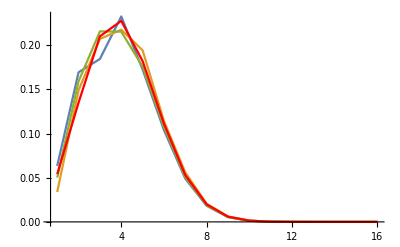

```mathematica
Show[ListLinePlot[Table[Nbysum@Rest[Table[Norm[Pkby[fs[[j]],k]]^2,{k,0,l}]],{j,nrep}],PlotRange->All],
ListLinePlot[VCExpected, DataRange->{1,l},PlotStyle->Red]]
```

### Noised FL

```mathematica
noiseprops={.05, .1, .2, .3, .4, .5, .8};
```

```mathematica
varnoiselist = (1/(1-#) -1)&/@noiseprops * Variance[fs[[1]]//Flatten]
```

{0.0526316,0.111111,0.25,0.428571,0.666667,1.,4.}

```mathematica
noisevecslist = Table[RandomVariate[NormalDistribution[0, Sqrt[varnoiselist[[i]]]], alpha^l], nrep,{i,Length@noiseprops}];
```

```mathematica
fnlist=Table[fs[[j]]+noisevecslist[[j,i]], {j,nrep},{i,Length@noiseprops}];
```

```mathematica
Table[r2[fnlist[[1,i]], fs[[1]]],{i,Length@noiseprops}]
```

{0.949812,0.900577,0.80114,0.698392,0.599393,0.498733,0.204478}

```mathematica
Do[Export[StringJoin["data/",fl,  "_f_","noised_", ToString[i],"_", ToString[noiseprops[[j]]],".tsv"],fnlist[[i,j]],"TSV"],{i,nrep},{j,Length@noiseprops}]
```

## Generate training samples

### Random sampling

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

```mathematica
trs=Table[RandomSample[Range[Length[sequences]],samplesizes[[i]]],{i,Length[samplesizes]}];
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
Do[Export[StringJoin[ "data/", "tr_",ToString[i],".tsv"],trs[[i]],"TSV"],{i,lg@trs}];
```

### Simulated mutagenesis

```mathematica
wt=ConstantArray[0,l];
```

```mathematica
wg=mks^(-1)//N
```

{1.,0.0625,0.00833333,0.00178571,0.000549451,0.000228938,0.000124875,0.0000874126,0.0000777001,0.0000874126,0.000124875,0.000228938,0.000549451,0.00178571,0.00833333,0.0625,1.}

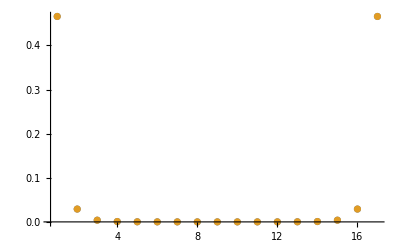

```mathematica
ListPlot[{Nbysum[mks^-1],Nbysum[wg]},PlotRange->All]
```

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];
seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];
hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,lg@seqsbyD}];
```

```mathematica
p=.1;
weights=(1-p)^(-#+l) p^# &/@hd;
```

```mathematica
(*We give minimum epistasis interpolation 1%, 10%, 50% and 90% of all data as training and use the rest of the data as test*)
trsmut=Table[RandomSample[weights->Range[alpha^l],Ceiling[i alpha^l]],{i,proportions}];
tstmut=Table[Complement[Range[alpha^l],trsmut[[i]]]//Flatten,{i,Length[proportions]}];
```

```mathematica
proportions//N
```

{0.00999451,0.0500031,0.100006,0.199997,0.300003,0.399994,0.5,0.600006,0.699997,0.800003,0.899994,0.949997,0.990005}

```mathematica
SortBy[hd[[trsmut[[1]]]]//Tally,First]
%[[All,2]]/mks[[;;Length[%]]]//N
```

{{0,1},{1,16},{2,120},{3,316},{4,136},{5,60},{6,4},{7,2}}

{1.,1.,1.,0.564286,0.0747253,0.0137363,0.0004995,0.000174825}

```mathematica
Do[Export[StringJoin["data/", "tr_mut_",ToString[i],".tsv"],trsmut[[i]],"TSV"],{i,lg@trsmut}];
```

```mathematica
proportions[[j]]
```

## Export data to GE

```mathematica
geWD=StringJoin["/Users/keitokiddo/Dropbox (UFL)/VC_revision/GE/", fl];
SetDirectory[geWD];
```

#### Random

```mathematica
scheme="random";
```

```mathematica
name = StringJoin[fl, "_", scheme,"_"];
```

```mathematica
Do[Export[StringJoin[name,ToString[i],"_",ToString[j],".txt"],Prepend[Transpose@{sequencesAA[[trs[[j]]]], fs[[i]][[trs[[j]]]], ConstantArray[0,trs[[j]]//Length], ConstantArray[fl, Length@trs[[j]]]},{"mut","f","v","condition"}],"CSV"],{i,nrep},{j,Length@trs}]
```

```mathematica
Flatten@Table[{StringReplace["dataf = CSV.read(\"file\")","file"->StringJoin[name,ToString[i],"_",ToString[j],".txt"]],StringReplace["d = prepdata(dataf, :mut, :sequence, \"WT\", :f, cname = :condition, vname = :v)", "WT"->wtAA],"@time mlin = nonepistatic_model(d)","@time m = fit(mlin, nk = 4, tol = 1e-14)",StringReplace["writedlm(\"b_#.tsv\",m[:b])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"a_#.tsv\",m[:a])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"yhat_#.tsv\",m[:yhat])","#"->StringJoin[name, ToString[i],"_",ToString[j]]]},{i,nrep},{j,Length@trs}];
```

```mathematica
Export[StringJoin[name, "terminal.txt"],Join[{StringReplace["cd(\"#\")","#"->geWD],"using CSV","using DataFrames","using GlobalEpistasis"},%]];
```

#### Noised

```mathematica
scheme="noised";
```

```mathematica
name = StringJoin[fl, "_", scheme,"_"]
```

2_16_SPR_noised_

```mathematica
J=3;
```

```mathematica
Do[Export[StringJoin[name,ToString[i],"_",ToString[j],".txt"],Prepend[Transpose@{sequencesAA[[trs[[j]]]], fnlist[[i,J]][[trs[[j]]]], ConstantArray[varnoiselist[[J]], Length@trs[[j]]], ConstantArray[fl, Length@trs[[j]]]},{"mut","f","v","condition"}],"CSV"],{i,nrep},{j,Length@trs}]
```

```mathematica
Flatten@Table[{StringReplace["dataf = CSV.read(\"file\")","file"->StringJoin[name,ToString[i],"_",ToString[j],".txt"]],StringReplace["d = prepdata(dataf, :mut, :sequence, \"WT\", :f, cname = :condition, vname = :v)", "WT"->wtAA],"@time mlin = nonepistatic_model(d)","@time m = fit(mlin, nk = 4, tol = 1e-14)",StringReplace["writedlm(\"b_#.tsv\",m[:b])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"a_#.tsv\",m[:a])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"yhat_#.tsv\",m[:yhat])","#"->StringJoin[name, ToString[i],"_",ToString[j]]]},{i,nrep},{j,Length@trs}];
```

```mathematica
Export[StringJoin[name, "terminal.txt"],Join[{StringReplace["cd(\"#\")","#"->geWD],"using CSV","using DataFrames","using GlobalEpistasis"},%]];
```

#### Mut

```mathematica
scheme="mut";
```

```mathematica
name = StringJoin[fl, "_", scheme,"_"]
```

2_16_SPR_mut_

```mathematica
Do[Export[StringJoin[name,ToString[i],"_",ToString[j],".txt"],Prepend[Transpose@{sequencesAA[[trs[[j]]]], fs[[i]][[trsmut[[j]]]], ConstantArray[0,Length@trsmut[[j]]], ConstantArray[fl, Length@trsmut[[j]]]},{"mut","f","v","condition"}],"CSV"],{i,nrep},{j,Length@trs}]
```

```mathematica
Flatten@Table[{StringReplace["dataf = CSV.read(\"file\")","file"->StringJoin[name,ToString[i],"_",ToString[j],".txt"]],StringReplace["d = prepdata(dataf, :mut, :sequence, \"WT\", :f, cname = :condition, vname = :v)", "WT"->wtAA],"@time mlin = nonepistatic_model(d)","@time m = fit(mlin, nk = 4, tol = 1e-14)",StringReplace["writedlm(\"b_#.tsv\",m[:b])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"a_#.tsv\",m[:a])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"yhat_#.tsv\",m[:yhat])","#"->StringJoin[name, ToString[i],"_",ToString[j]]]},{i,nrep},{j,Length@trs}];
```

```mathematica
Export[StringJoin[name, "terminal.txt"],Join[{StringReplace["cd(\"#\")","#"->geWD],"using CSV","using DataFrames","using GlobalEpistasis"},%]];
```

## Import GE results

#### Bulk import GE results

```mathematica
deg=2; (*M-spline basis degree, I-spline degree is deg+1*)
elem=5; (*Number of splines in finished basis*)
knots=Range[0,1,1/(elem-deg)];
knots=Join[ConstantArray[knots[[1]],deg],knots,ConstantArray[knots[[-1]],deg]];
Table[Integrate[BSplineBasis[{deg,knots},i,x],x],{i,0,Length[knots]-deg-2}];
ReplacePart[%,
{{1,1,1,1}->BSplineBasis[{deg,knots},0,0]x,{-1,1}->Join[%[[-1,1]] ,{{(%[[-1]]/.x->1)+BSplineBasis[{deg,knots},Length[knots]-deg-2,1](x-1),x>1}}]}];
(basis=%/%[[All,2]]//Simplify);
transform[phi_,a_]:=First[a]+basis.Rest[a]/.{x->phi}
```

```mathematica
geprefix=fl;
```

```mathematica
geWD=StringJoin["/Users/keitokiddo/Dropbox (UFL)/VC_revision/GE/", fl];
SetDirectory[geWD];
```

```mathematica
Directory[]
```

/Users/keitokiddo/Dropbox (UFL)/VC_revision/GE/2_16_SPR

```mathematica
schemes = {"random", "noised", "mut"};
```

```mathematica
names =StringJoin[fl, "_", #,"_"]&/@schemes;
```

```mathematica
pdsGE=Table[{},nschemes,nrep, Length[trs]];
```

```mathematica
Do[pdsGE[[k]][[i,j]]=Module[{y,b,a,yhat,spline,PossibleEffects,FactorMatrix,SortedEffects,Effects,coeffsAll, phige},
b=Transpose[Import[StringReplace["b_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
a=Transpose[Import[StringReplace["a_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
yhat=Transpose[Import[StringReplace["yhat_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
spline[x_]:=transform[x,a];
PossibleEffects=Complement[Join[Tuples[{Range[l],AA}],{{geprefix}}],Thread[{Range[l],Characters[wtAA]}]];

FactorMatrix=Table[Join[{geprefix},Thread[{Range[l],Characters[sequencesAA[[k]]]}]],{k,trs[[j]]}];SortedEffects=SortBy[Transpose[{PossibleEffects,Table[Min[Position[Flatten[FactorMatrix,1],PossibleEffects[[i]]]],{i,Length[PossibleEffects]}]}],Last];Effects=Pick[SortedEffects[[All,1]],NumberQ/@SortedEffects[[All,2]]];Effects=Pick[SortedEffects[[All,1]],NumberQ/@SortedEffects[[All,2]]];coeffsAll=MapPartialVal[(FromDigits[#,alpha]&/@(Effects[[1;;]]/.AAtoDigitRules)) -alpha+1,b[[2;;]],alpha*l];
phige = nullonehot.Join[{b[[1]]},coeffsAll];
spline/@phige
],{k,3}, {i,nrep},{j,13}]
```

```mathematica
pdsGE//Dimensions
```

{3,3,13,65536}

```mathematica
SetDirectory[StringJoin[wd]];
```

```mathematica
pdsGE>> "pdsGE.m";
```

```mathematica
(*pdsGE = Import[StringJoin[wd,"/pdsGE.m"]];*)
```

## VC

## glmnet

## Plotting

### Import FL

```mathematica
fs=Table[{},nrep];
Do[fs[[i]]=Import[StringJoin["data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
fns=Table[{},nrep];
Do[fns[[i]]=Import[StringJoin["data/",fl,  "_f_","noised_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
```

### Import training samples

```mathematica
trs=Table[{},Length@proportions];
Do[trs[[i]]=Import[StringJoin["data/", "tr_",ToString[i],".tsv"]]//Flatten,{i,Length@proportions}]
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
```

```mathematica
trsmut=Table[{},Length@proportions];
Do[trsmut[[i]]=Import[StringJoin["data/", "tr_mut_",ToString[i],".tsv"]]//Flatten,{i,lg@trsmut}]
ttsmut=Table[Complement[Range[alpha^l],trsmut[[i]]],{i,Length[trsmut]}];
```

### Import VC results

```mathematica
wd=StringJoin[hd,fl];
SetDirectory[wd];
```

```mathematica
pdsVC=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="vc";
```

```mathematica
Do[
If[schemes[[k]]=="noised", name=StringRiffle[{fl, schemes[[k]], modelname, i,noiseprops[[J]],  j}, "_"],
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"]];
pdsVC[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

Import::nffil: File out/2_16_DEN_mut_vc_1_4.tsv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File out/2_16_DEN_mut_vc_1_5.tsv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File out/2_16_DEN_mut_vc_1_6.tsv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

```mathematica
Table[Length[pdsVC[[k,i,j]]],{k,nschemes},{i,nrep}, {j,Length@proportions}]
```

{{{65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536},{65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536},{65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536}},{{65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536},{65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536},{65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536}},{{65536,65536,65536,1,1,1,1,1,1,1,1,1,1},{65536,65536,65536,1,1,1,1,1,1,1,1,1,1},{65536,65536,65536,1,1,1,1,1,1,1,1,1,1}}}

### Import GE results

#### Bulk import GE results

```mathematica
deg=2; (*M-spline basis degree, I-spline degree is deg+1*)
elem=5; (*Number of splines in finished basis*)
knots=Range[0,1,1/(elem-deg)];
knots=Join[ConstantArray[knots[[1]],deg],knots,ConstantArray[knots[[-1]],deg]];
Table[Integrate[BSplineBasis[{deg,knots},i,x],x],{i,0,Length[knots]-deg-2}];
ReplacePart[%,
{{1,1,1,1}->BSplineBasis[{deg,knots},0,0]x,{-1,1}->Join[%[[-1,1]] ,{{(%[[-1]]/.x->1)+BSplineBasis[{deg,knots},Length[knots]-deg-2,1](x-1),x>1}}]}];
(basis=%/%[[All,2]]//Simplify);
transform[phi_,a_]:=First[a]+basis.Rest[a]/.{x->phi}
```

```mathematica
geprefix=fl;
```

```mathematica
geWD=StringJoin["/Users/keitokiddo/Dropbox (UFL)/VC_revision/GE/", fl];
SetDirectory[geWD];
```

```mathematica
schemes = {"random", "noised", "mut"};
```

```mathematica
names =StringJoin[fl, "_", #,"_"]&/@schemes;
```

```mathematica
pdsGE=Table[{},nschemes,nrep, Length[trs]];
```

```mathematica
Do[pdsGE[[k]][[i,j]]=Module[{y,b,a,yhat,spline,PossibleEffects,FactorMatrix,SortedEffects,Effects,coeffsAll, phige},
b=Transpose[Import[StringReplace["b_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
a=Transpose[Import[StringReplace["a_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
yhat=Transpose[Import[StringReplace["yhat_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
spline[x_]:=transform[x,a];
PossibleEffects=Complement[Join[Tuples[{Range[l],AA}],{{geprefix}}],Thread[{Range[l],Characters[wtAA]}]];

FactorMatrix=Table[Join[{geprefix},Thread[{Range[l],Characters[sequencesAA[[k]]]}]],{k,trs[[j]]}];SortedEffects=SortBy[Transpose[{PossibleEffects,Table[Min[Position[Flatten[FactorMatrix,1],PossibleEffects[[i]]]],{i,Length[PossibleEffects]}]}],Last];Effects=Pick[SortedEffects[[All,1]],NumberQ/@SortedEffects[[All,2]]];Effects=Pick[SortedEffects[[All,1]],NumberQ/@SortedEffects[[All,2]]];coeffsAll=MapPartialVal[(FromDigits[#,alpha]&/@(Effects[[1;;]]/.AAtoDigitRules)) -alpha+1,b[[2;;]],alpha*l];
phige = nullonehot.Join[{b[[1]]},coeffsAll];
spline/@phige
],{k,3}, {i,nrep},{j,13}]
```

```mathematica
pdsGE//Dimensions
```

{3,3,13,65536}

```mathematica
SetDirectory[StringJoin[wd]];
```

```mathematica
pdsGE>> "pdsGE.m";
```

```mathematica
(*pdsGE = Import[StringJoin[wd,"/pdsGE.m"]];*)
```

### Import glmnet results

#### 2way

```mathematica
pds2way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="2way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds2way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

```mathematica
pds2way//Dimensions
```

{3,3,13,65536}

#### 3way

```mathematica
pds3way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="3way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds3way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

```mathematica
pds3way//Dimensions
```

{3,3,13,65536}

#### Combine

```mathematica
pdsAll={pdsVC, pdsGE, pds2way,pds3way};
nmodels=Length[pdsAll];
```

### Plot Random

#### Plotting R2 curves

```mathematica
colors={Black,Gray,RGBColor@@({208,209,230}/255),RGBColor@@({51,160,44}/255),RGBColor@@({140,180,227}/255)};
fontsize=20;
fstyle=Table[{GrayLevel[.3],Thickness[.006]},4];
pt=.2;
style={#,Thickness[.004],PointSize[pt]}&/@colors;
```

```mathematica
modellabs={Style["VC regression",FontFamily->"Helvetica"],
Style["Global epistasis",FontFamily->"Helvetica"],
Style["Pairwise regression",FontFamily->"Helvetica"],
Style["Three-way regression",FontFamily->"Helvetica"]};
```

```mathematica
(*modellabs={Style["VC regression",FontFamily->"Helvetica"],
Style["Additive",FontFamily->"Helvetica"],
Style["Global epistasis",FontFamily->"Helvetica"],
Style["Pairwise",FontFamily->"Helvetica"],
Style["Three-way",FontFamily->"Helvetica"]};
modelnames={"VC regression","Additive","Global epistasis","Pairwise","Three-way"};*)
```

```mathematica
pds=pdsAll[[All, 1]];
```

```mathematica
pds//Dimensions
```

{4,3,13,65536}

```mathematica
pds[[1]]//Dimensions
```

{3,13,65536}

```mathematica
k=1;
Table[Length[pds[[k,i,j]]],{i,nrep},{j,nprop}]
```

{{65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536},{65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536},{65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536,65536}}

```mathematica
R2s=Table[r2[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
```

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

```mathematica
plotdat=Table[Table[{Around[proportions[[j]],0],Around[Mean[R2s[[k]][[All,j]]],StandardDeviation[R2s[[k]][[All,j]]]]},{j,Length[proportions]}],{k,nmodels}];
```

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

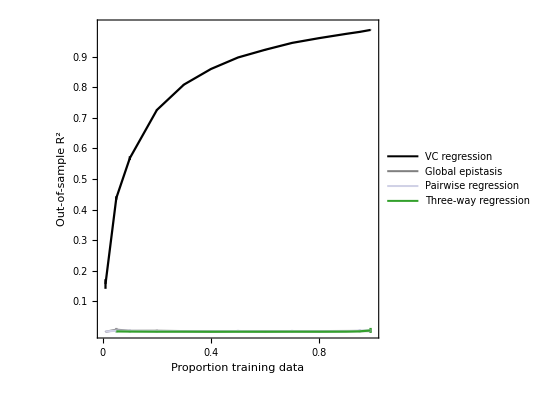

```mathematica
figr2=ListPlot[
plotdat,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
Frame->True,
PlotStyle->style,
FrameStyle->fstyle,
FrameTicks->{{Range[.1,.9,.1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Out-of-sample "Superscript[R,2]},
Joined->True,
ClippingStyle->None,
ImageSize->400,PlotLegends->Placed[LineLegend[Automatic,modellabs,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],{.75,.25}]]
```

Add more points between 1 and 10 percent

### Plot noised

```mathematica
colors={Black,Gray,RGBColor@@({208,209,230}/255),RGBColor@@({51,160,44}/255),RGBColor@@({140,180,227}/255)};
fontsize=20;
fstyle=Table[{GrayLevel[.3],Thickness[.006]},4];
pt=.2;
style={#,Thickness[.004],PointSize[pt]}&/@colors;
```

#### Reconstruction of training data under noise

```mathematica
pds=pdsAll[[All,2]];
```

```mathematica
R2s=Table[r2[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
```

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

```mathematica
MSEs=Table[mse[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
```

```mathematica
plotdat=Table[Table[{Around[proportions[[j]],0],Around[Mean[R2s[[k]][[All,j]]],StandardDeviation[R2s[[k]][[All,j]]]]},{j,Length[proportions]}],{k,nmodels}];
```

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

```mathematica
modellabs={Style["VC regression",FontFamily->"Helvetica"],
Style["Global epistasis",FontFamily->"Helvetica"],
Style["Pairwise regression",FontFamily->"Helvetica"],
Style["Three-way regression",FontFamily->"Helvetica"]};
```

```mathematica
style={{GrayLevel[0],Thickness[0.004],PointSize[0.2]},{GrayLevel[0.5],Thickness[0.004],PointSize[0.2]},{RGBColor[Rational[208, 255], Rational[209, 255], Rational[46, 51]],Thickness[0.004],PointSize[0.2]},{RGBColor[Rational[1, 5], Rational[32, 51], Rational[44, 255]],Thickness[0.004],PointSize[0.2]},{RGBColor[Rational[28, 51], Rational[12, 17], Rational[227, 255]],Thickness[0.004],PointSize[0.2]}};
```

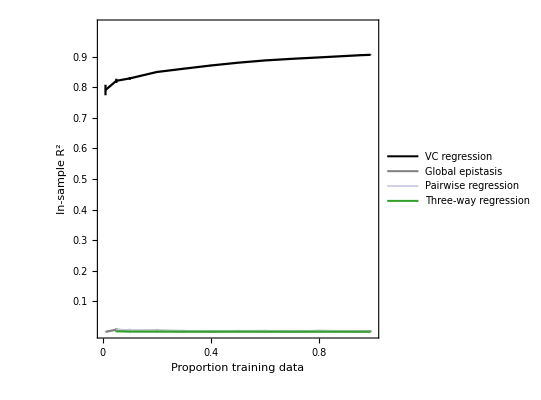

```mathematica
ListPlot[
plotdat,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
Frame->True,
PlotStyle->style,
FrameStyle->fstyle,
FrameTicks->{{Range[.1,.9,.1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","In-sample "Superscript[R,2]},
Joined->True,
ClippingStyle->None,
ImageSize->400,PlotLegends->Placed[LineLegend[Automatic,modellabs,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],{.75,.25}]]
```

### Plot mut

```mathematica
pds=pdsAll[[All,3]];
```

```mathematica
j=2;
proportions[[j]]//N
ttsmut[[j]]//Length
tstbyD=Table[Intersection[ttsmut[[j]],seqbyhd[[d]]], {d, l+1}];
```

0.0500031

62259

```mathematica
Length/@tstbyD;
 %/mks//N;
trsdensity = 1-%
```

{1.,1.,1.,1.,0.838462,0.192308,0.0227273,0.00236014,0.0003885,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Position[#=={}&/@tstbyD,False][[1]]//First ;
dmin=%-1
```

4

```mathematica
R2s=Table[r2[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}]
```

{{{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{0.763814,0.783288,0.743283},{0.715966,0.721729,0.699139},{0.511499,0.517596,0.468055},{0.287818,0.309193,0.214127},{0.123162,0.154693,0.059239},{0.034277,0.0676899,0.00639965},{0.0033488,0.0222755,0.000122864},{0.000864755,0.00198582,0.000035385},{0.00459802,0.00215611,0.00346028},{0.00205821,0.00684794,0.0208893},{0.0063925,0.00266322,0.0648406},{0.136044,0.000557094,0.0948541},{{},{},{}}},{{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{4.25437×10^-6,0.00428207,0.000825475},{0.00113954,0.000096858,0.000795114},{0.00226366,0.0000535299,0.00256321},{0.00191728,0.0000309794,0.00463554},{0.000638639,0.000056492,0.00531192},{0.0000140048,0.00019446,0.00340065},{0.000315347,0.000638108,0.00111412},{0.00209845,0.00142084,7.72056×10^-6},{0.0071848,0.0016792,0.000692749},{0.0112049,0.00266302,0.00142736},{0.000295931,0.00959618,0.000102553},{0.100607,0.0307844,0.0424488},{{},{},{}}},{{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{0.00499979,0.00758911,0.00369308},{0.00102032,0.00911657,0.00205922},{0.00203785,0.00540974,0.000276093},{0.00151002,0.00386906,0.000186578},{0.00141937,0.00413348,0.000621465},{0.00233437,0.00571821,0.000181219},{0.00491041,0.00606855,0.000222418},{0.00856901,0.00328661,0.00257627},{0.0123916,0.000405662,0.00711015},{0.018746,3.72847×10^-7,0.0155382},{0.0318755,0.00341561,0.047348},{0.0426739,0.0698965,0.14278},{{},{},{}}},{{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{0.00147415,0.0099245,0.00804716},{0.0000218527,0.00157976,0.00129952},{0.0000998747,6.67292×10^-6,0.000544774},{0.000027026,6.41919×10^-6,0.00437894},{0.000160676,0.00116487,0.00556399},{0.000263757,0.0051328,0.00335721},{0.000334729,0.00820089,0.000535724},{0.000210912,0.00580619,0.00049349},{4.66647×10^-7,0.000997384,0.00458398},{0.000101262,0.000336099,0.0144082},{0.000572185,0.000489822,0.0485551},{0.0189419,0.0125847,0.125787},{{},{},{}}}}

```mathematica
plotdat=Table[{Around[d,0],Around[Mean[R2s[[k]][[d+1]]],StandardDeviation[R2s[[k]][[d+1]]]]},{k,nmodels},{d,dmin,l}];
```

StandardDeviation::shlen: The argument {{},{},{}} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

```mathematica
plotsampling=ListPlot[trsdensity,
BaseStyle->{FontSize->fontsize},
DataRange->{0,l},
PlotRange->{{0,l},{0,1}},
Frame->True,
PlotStyle->{GrayLevel[0],Thickness[0.004],PointSize[0.02]},
FrameStyle->fstyle,
FrameTicks->{{Range[0,1,.1],False},{Range[0,l],False}},FrameLabel->{"Distance to WT","Sampling density"},
PlotRangeClipping->False,
AspectRatio->.75,
ImageSize->400];
```

```mathematica
plotr2d=ListPlot[
plotdat,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
PlotRange->{{0,l},{0,1}},
Frame->True,
PlotStyle->style,
FrameStyle->fstyle,
FrameTicks->{{Range[.1,.9,.1],False},{Range[0,l],False}},FrameLabel->{"Hamming Distance to WT","Out-of-sample "Superscript[R,2]},
Joined->True,
PlotRangeClipping->False,
ImageSize->400,PlotLegends->Placed[LineLegend[Automatic,modellabs,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],{.75,.25}]];
```

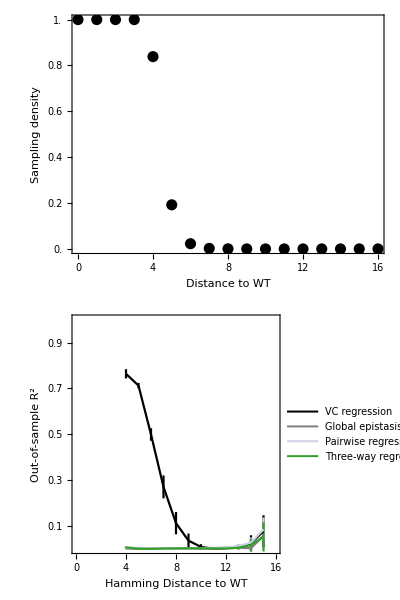

```mathematica
Grid[{{plotsampling},{plotr2d}}]
```